```mathematica
Blend[{White, Darker@Purple},#]&
```

```mathematica
ClearAll[a,b,c,d, Equazioni]
```

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
(*Needs["VectorAnalysis`"]*)
system=GetNDSolveProblem["LotkaVolterra"];
invts=system["Invariants"];
time=system["TimeData"];
vars=system["DependentVariables"];
```

```mathematica
LotkaVolterraPlot[sol_,vars_,time_,opts___?OptionQ]:=Module[{commonopts,data,data1,data2,ifuns,lplot,pplot},ifuns=First[vars/.sol];
data1=Part[ifuns,1,0]["ValuesOnGrid"];
data2=Part[ifuns,2,0]["ValuesOnGrid"];
data=Transpose[{data1,data2}];
commonopts=Sequence[Axes->False,Frame->True,FrameLabel->Join[Map[TraditionalForm,vars],{None,None}],RotateLabel->False, PlotRange-> All];
lplot=ListPlot[data,Evaluate[FilterRules[{opts},Options[ListPlot]]],PlotStyle->{PointSize[0.02],RGBColor[0,1,0]},Evaluate[commonopts]];
pplot=ParametricPlot[Evaluate[ifuns],time,Evaluate[FilterRules[{opts},Options[ParametricPlot]]],Evaluate[commonopts]];
Show[lplot,pplot]];
```

```mathematica
LotkaVolterraPlotLine[sol_,vars_,time_,opts___?OptionQ]:=Module[{commonopts,data,data1,data2,ifuns,lplot,pplot},ifuns=First[vars/.sol];
data1=Part[ifuns,1,0]["ValuesOnGrid"];
data2=Part[ifuns,2,0]["ValuesOnGrid"];
data=Transpose[{data1,data2}];
commonopts=Sequence[Axes->False,Frame->True,FrameLabel->Join[{"v(t)","I(t)"},{None,None}],RotateLabel->True, PlotRange->All,PlotRangePadding->0.1, LabelStyle->{Directive[Black,22],FontFamily->"Times"}, PlotStyle->{Directive[Gray,Thick]},  AspectRatio->1];
pplot=ParametricPlot[Evaluate[ifuns],time,Evaluate[FilterRules[{opts},Options[ParametricPlot]]],Evaluate[commonopts]];
Show[pplot]];
```

```mathematica
LotkaVolterraPlotStable[sol_,vars_,time_,stablepoints_, opts___?OptionQ]:=Module[{commonopts,data,data1,data2,ifuns,lplot,pplot,datastab},ifuns=First[vars/.sol];
data1=Part[ifuns,1,0]["ValuesOnGrid"];
data2=Part[ifuns,2,0]["ValuesOnGrid"];
data=Transpose[{data1,data2}];
datastab=stablepoints;
commonopts=Sequence[Axes->False,Frame->True,FrameLabel->Join[{"v(t)","I(t)"},{None,None}],RotateLabel->True, PlotRange->All,PlotRangePadding->0.1, LabelStyle->{Directive[Black,22],FontFamily->"Times"}, PlotStyle->{Directive[Gray,Thick]},  AspectRatio->1];
lplot=ListPlot[datastab,Evaluate[FilterRules[{opts},Options[ListPlot]]],PlotStyle->{PointSize[0.03],Red}, Evaluate[commonopts] ];
pplot=ParametricPlot[Evaluate[ifuns],time,Evaluate[FilterRules[{opts},Options[ParametricPlot]]],Evaluate[commonopts]];
Show[pplot, lplot]];
```

```mathematica
LotkaVolterraPlotTime[sol_,vars_,time_,opts___?OptionQ]:=Module[{commonopts,data,data1,data2,ifuns,lplot,pplot},ifuns=First[vars/.sol];
data1=Part[ifuns,1,0]["ValuesOnGrid"];
data2=Part[ifuns,2,0]["ValuesOnGrid"];
data=Transpose[{data1,data2}];
commonopts=Sequence[Axes->False,Frame->True,FrameLabel->Join[Map[TraditionalForm,vars],{None,None}],RotateLabel->False];
lplot=ListPlot[data1,,Evaluate[FilterRules[{opts},Options[ListPlot]]],PlotStyle->{PointSize[0.02],RGBColor[0,1,0]},Evaluate[commonopts]];
Show[lplot,pplot]];
```

```mathematica
(*JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
JacobianDeterminant[f_List?VectorQ,x_List]:=Det[JacobianMatrix[f,x]]/;Equal@@(Dimensions/@{f,x})*)
```

```mathematica
(***** ******* ******* ******* ******* ****)
(***** ******* CODE  ******* ****)
(***** ******* ******* ******* ******* ****)
```

```mathematica
ClearAll[a,b,c,d,aA,bA,cA,dA,aS,bS,cS,dS, n, m, mS, mA, pars, n];
```

```mathematica
totalDays=60;
AvgAmountAI={};
AvgAmountAV={};
AvgFracAI={};
AvgFracAV={};
listFractimeI={};
listFractimeV={};
listAmountI={};
listAmountV={};
InitConditAwakeAll={{0,0}};

(*Jlist={0.2, 0.3, 0.4,0.5,0.6, 0.7,0.8,0.9,1};*)
Hlist={0,2,4,6,8,10,12,14,16,18,20,22,24};
Jlist={0.2, 0.3,0.4,0.5,0.6,0.7,0.8,0.9};
(*Hlist={2,6,8,12,22};*)
maxparJ=Length[Jlist]+1;
maxparH=Length[Hlist]+1;
pars=Jlist;
```

```mathematica
For[H=1,H<maxparH,H++,Print[H];
AvgAmountI={};
AvgAmountV={};
  AvgFracI={};
  AvgFracV={};
  InitConditAwakeAll={{0,0}};
For[J=1,J<maxparJ,J++,Print[J];
aA=1.5;
dA=0.15;
cA=1;(*J*0.2*)
bA=5;(*N[Hlist[[H]]];*)
mA=0.15;

aS=aA*N[Jlist[[J]]];
dS=0.15;
cS=1;
bS=5; (*N[Hlist[[H]]];*)
mS=0.15;

tawake=N[Hlist[[H]]];
tsleep=24-tawake;
Print[StringJoin["aS ", ToString[aS], " TAwake ",ToString[tawake]]];

Equazioni = {
Derivative[1][Virus][t] == Virus[t]*(a-m) -b*Immune[t]*Virus[t] ,
    Derivative[1][Immune][t] == -d*Immune[t]+b*c Virus[t] 
};
InitCondit0= {(a-m)/b, (d*(a-m))/((b*b)*c)}/.a->aS/.b->bS/.c->cS/.d->dS/.m->mS;
InitConditAwake = { (a-m)/b, (d*(a-m))/((b*b)*c)}/.a->aA/.b->bA/.c->cA/.d->dA/.m->mA;
InitConditFOR= {Immune[0] == I0, Virus[0] == V0};

n=0;
(*TransPoint={{0,0}};*)
ttot={0};	
For[n=0,n<totalDays*2,n++,
	    If[n==0,
			IC=InitConditFOR/.I0-> InitCondit0 [[1]]/.V0-> InitCondit0 [[2]]; 
				TransPoint={{IC[[2]][[2]],IC[[1]][[2]]}};,
			IC=InitConditFOR/.I0-> ifuns[[2]][[0]][tm]/.V0-> ifuns[[1]][[0]][tm]; 
				AppendTo[TransPoint,{IC[[2]][[2]],IC[[1]][[2]]}] ;
	];				  
	     If[Mod[n,2]==0,
			eq=Equazioni/.a->aA/.b->bA/.c->cA/.d->dA/. m->mA; tm=tawake; AppendTo[ttot,ttot[[-1]]+tawake],
			eq=Equazioni/.a->aS/.b->bS/.c->cS/.d->dS/. m->mS; tm=tsleep ; AppendTo[ttot,ttot[[-1]]+tsleep]
	];
	(*Print[eq];*)
	(*Print[TransPoint];*)
	MergedSysFOR=Join[eq,IC];
	(*Print[MergedSysFOR];*)
          mysolFOR=NDSolve[MergedSysFOR,
	         	{Virus[t],Immune[t]},
			{t,0,tm}
			];
	ifuns=First[{Virus[t],Immune[t]}/.mysolFOR] ;
	(*Print[ifuns[[1]][[0]][0]];
	Print[ifuns[[2]][[0]][0]];
	Print[n]*)
	If[n==0,
	VirusData=Part[ifuns,1,0]["ValuesOnGrid"];ImmuneData=Part[ifuns,2,0]["ValuesOnGrid"]; ,
	VirusData=Flatten[Append[VirusData,Part[ifuns,1,0]["ValuesOnGrid"]]];ImmuneData=Flatten[Append[ImmuneData,Part[ifuns,2,0]["ValuesOnGrid"]]]; 
	];
	If[n==0,
	VirusData2= Flatten[Table[Virus[t]/.mysolFOR, {t,0,tm,1./60}]];
	ImmuneData2= Flatten[Table[Immune[t]/.mysolFOR, {t,0,tm,1./60}]]; ,
	VirusData2=Flatten[Append[VirusData2, Table[Virus[t]/.mysolFOR, {t,1./60,tm,1./60}]]];
	ImmuneData2=Flatten[Append[ImmuneData2, Table[Immune[t]/.mysolFOR, {t,1./60,tm,1./60}]]]; 
	];
];
Final=InitConditFOR/.I0-> ifuns[[2]][[0]][tm]/.V0-> ifuns[[1]][[0]][tm]; 
AppendTo[TransPoint,{Final[[2]][[2]],Final[[1]][[2]]}] ;
ttot2=Range[0,ttot[[-1]],1./60];

FractimeV={};
       AmountV={};
FractimeI={}; 
       AmountI={};
(*Print[Length[VirusData2]];*)

(*I take the data of value of virus in time, and for each dayI cacluclate how many timeoints are below InitConditAwake. 1440= #minutes in a day *);
For[k=50,k<totalDays,k++,
FractimeI=Append[FractimeI,Length[Select[ImmuneData2[[1+(60*24*(k-1));;1+(60*24*k)]],#<InitConditAwake[[1]]&]]/1440.];
FractimeV=Append[FractimeV,Length[Select[VirusData2[[1+(60*24*(k-1));;1+(60*24*k)]],#<InitConditAwake[[2]]&]]/1440.];
];
(*Print[FractimeI];
Print[FractimeV];*)
AvgFracI=Append[AvgFracI,{tawake,N[Jlist[[J]]],Mean[FractimeI]}];
AvgFracV=Append[AvgFracV,{tawake,N[Jlist[[J]]],Mean[FractimeV]}];

(*I take the data of value of virus in time, and for each dayI calc avg value. 1440= #minutes in a day *)
For[k=50,k<totalDays,k++,
AmountI=Append[AmountI,Mean[ImmuneData2[[1+(60*24*(k-1));;1+(60*24*k)]]/InitConditAwake[[1]]]];
AmountV=Append[AmountV,Mean[VirusData2[[1+(60*24*(k-1));;1+(60*24*k)]]/InitConditAwake[[2]]]];
];
(*Print[AmountI];
Print[AmountV];*)
	AvgAmountI=Append[AvgAmountI,{tawake,N[Jlist[[J]]],Mean[AmountI]}];
	AvgAmountV=Append[AvgAmountV,{tawake,N[Jlist[[J]]],Mean[AmountV]}];
	InitConditAwakeAll=Append[InitConditAwakeAll,InitConditAwake];

listFractimeI=Append[listFractimeI,{tawake,N[Jlist[[J]]],DeleteDuplicates[Floor[FractimeI*100.]]}];
listFractimeV=Append[listFractimeV,{tawake,N[Jlist[[J]]],DeleteDuplicates[Floor[FractimeV*100.]]}];
listAmountI=Append[listAmountI,{tawake,N[Jlist[[J]]],DeleteDuplicates[Floor[AmountI*100.]]}];
listAmountV=Append[listAmountV,{tawake,N[Jlist[[J]]],DeleteDuplicates[Floor[AmountV*100.]]}];
];

For[i=1,i<maxparJ,i++,
AvgAmountAI=Append[AvgAmountAI,AvgAmountI[[i]]]; (*[[2;;]]]*)
AvgAmountAV=Append[AvgAmountAV,AvgAmountV[[i]]];
  AvgFracAI=Append[AvgFracAI,AvgFracI[[i]]];
  AvgFracAV=Append[AvgFracAV,AvgFracV[[i]]];
];
(*AvgAmountAV=Append[AvgAmountAV,AvgAmountV];
  AvgFracAI=Append[AvgFracAI,AvgFracI];
  AvgFracAV=Append[AvgFracAV,AvgFracV];*)
]
```

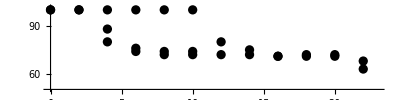

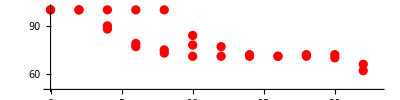

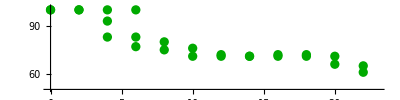

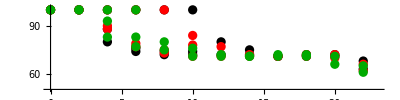

```mathematica
listFractimeI
T102=Table[{listFractimeI[[1;;;;4]][[i]][[1]],listFractimeI[[1;;;;4]][[i]][[3]][[1]]}, {i,1,Length[listFractimeI[[1;;;;4]]]} ];
T202=Table[{listFractimeI[[1;;;;4]][[i]][[1]],
			If[Length[listFractimeI[[1;;;;4]][[i]][[3]]]>1,listFractimeI[[1;;;;4]][[i]][[3]][[2]],-1]},  {i,1,Length[listFractimeI[[1;;;;4]]]} ];
T104=Table[{listFractimeI[[2;;;;4]][[i]][[1]],listFractimeI[[2;;;;4]][[i]][[3]][[1]]}, {i,1,Length[listFractimeI[[1;;;;4]]]} ];
T204=Table[{listFractimeI[[2;;;;4]][[i]][[1]],
			If[Length[listFractimeI[[2;;;;4]][[i]][[3]]]>1,listFractimeI[[2;;;;4]][[i]][[3]][[2]],-1]},  {i,1,Length[listFractimeI[[1;;;;4]]]} ]
T106=Table[{listFractimeI[[3;;;;4]][[i]][[1]],listFractimeI[[3;;;;4]][[i]][[3]][[1]]}, {i,1,Length[listFractimeI[[1;;;;4]]]} ];
T206=Table[{listFractimeI[[3;;;;4]][[i]][[1]],
			If[Length[listFractimeI[[3;;;;4]][[i]][[3]]]>1,listFractimeI[[3;;;;4]][[i]][[3]][[2]],-1]},  {i,1,Length[listFractimeI[[1;;;;4]]]} ]

P1=ListPlot[{T102,T202}, PlotRange->{{0,23},{50,102}}, PlotStyle->{Black}, AspectRatio->0.25]
P2=ListPlot[{T104,T204}, PlotRange->{{0,23},{50,102}}, PlotStyle->{Red}, AspectRatio->0.25]
P3=ListPlot[{T106,T206}, PlotRange->{{0,23},{50,102}}, PlotStyle->{Darker[Green]}, AspectRatio->0.25]
Show[P1,P2,P3]
```

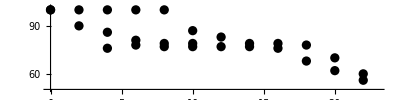

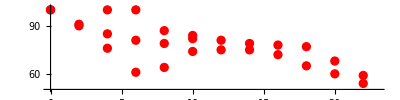

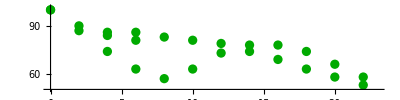

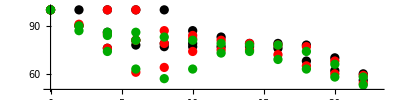

```mathematica
listFractimeV
T102V=Table[{listFractimeV[[1;;;;4]][[i]][[1]],listFractimeV[[1;;;;4]][[i]][[3]][[1]]}, {i,1,Length[listFractimeV[[1;;;;4]]]} ];
T202V=Table[{listFractimeV[[1;;;;4]][[i]][[1]],
			If[Length[listFractimeV[[1;;;;4]][[i]][[3]]]>1,listFractimeV[[1;;;;4]][[i]][[3]][[2]],-1]},  {i,1,Length[listFractimeV[[1;;;;4]]]} ];
T104V=Table[{listFractimeV[[2;;;;4]][[i]][[1]],listFractimeV[[2;;;;4]][[i]][[3]][[1]]}, {i,1,Length[listFractimeV[[1;;;;4]]]} ];
T204V=Table[{listFractimeV[[2;;;;4]][[i]][[1]],
			If[Length[listFractimeV[[2;;;;4]][[i]][[3]]]>1,listFractimeV[[2;;;;4]][[i]][[3]][[2]],-1]},  {i,1,Length[listFractimeV[[1;;;;4]]]} ]
T106V=Table[{listFractimeV[[3;;;;4]][[i]][[1]],listFractimeV[[3;;;;4]][[i]][[3]][[1]]}, {i,1,Length[listFractimeV[[1;;;;4]]]} ];
T206V=Table[{listFractimeV[[3;;;;4]][[i]][[1]],
			If[Length[listFractimeV[[3;;;;4]][[i]][[3]]]>1,listFractimeV[[3;;;;4]][[i]][[3]][[2]],-1]},  {i,1,Length[listFractimeV[[1;;;;4]]]} ]

P1=ListPlot[{T102V,T202V}, PlotRange->{{0,23},{50,102}}, PlotStyle->{Black}, AspectRatio->0.25]
P2=ListPlot[{T104V,T204V}, PlotRange->{{0,23},{50,102}}, PlotStyle->{Red}, AspectRatio->0.25]
P3=ListPlot[{T106V,T206V}, PlotRange->{{0,23},{50,102}}, PlotStyle->{Darker[Green]}, AspectRatio->0.25]
Show[P1,P2,P3]
```

```mathematica
Min[Table[AvgAmountAI[[i]][[3]], {i,1,Length[AvgAmountAI]}]]
Min[Table[AvgAmountAV[[i]][[3]], {i,1,Length[AvgAmountAV]}]]
Max[Table[AvgAmountAI[[i]][[3]], {i,1,Length[AvgAmountAI]}]]
Max[Table[AvgAmountAV[[i]][[3]], {i,1,Length[AvgAmountAV]}]]
Min[Table[AvgFracAI[[i]][[3]], {i,1,Length[AvgFracAI]}]]
Min[Table[AvgFracAV[[i]][[3]], {i,1,Length[AvgFracAV]}]]
Max[Table[AvgFracAI[[i]][[3]], {i,1,Length[AvgFracAI]}]]
Max[Table[AvgFracAV[[i]][[3]], {i,1,Length[AvgFracAV]}]]
```

```mathematica
Mean[Table[AvgAmountAI[[i]][[3]], {i,1,Length[AvgAmountAI]}]]
Mean[Table[AvgAmountAV[[i]][[3]], {i,1,Length[AvgAmountAV]}]]
Mean[Table[AvgFracAI[[i]][[3]], {i,1,Length[AvgFracAI]}]]
Mean[Table[AvgFracAV[[i]][[3]], {i,1,Length[AvgFracAV]}]]
StandardDeviation[Table[AvgAmountAI[[i]][[3]], {i,1,Length[AvgAmountAI]}]]
StandardDeviation[Table[AvgAmountAV[[i]][[3]], {i,1,Length[AvgAmountAV]}]]
StandardDeviation[Table[AvgFracAI[[i]][[3]], {i,1,Length[AvgFracAI]}]]
StandardDeviation[Table[AvgFracAV[[i]][[3]], {i,1,Length[AvgFracAV]}]]
```

0.777714

0.777644

0.685517

0.661419

0.219517

0.219479

0.275646

0.270679

```mathematica
AvgAmountAI
```

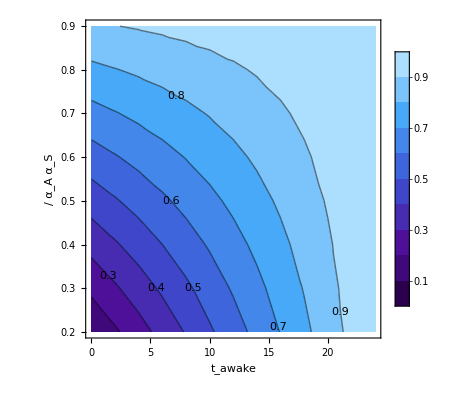

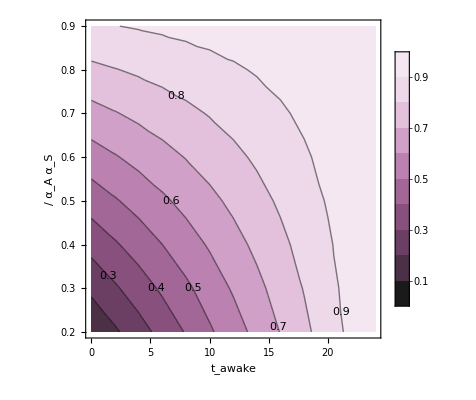

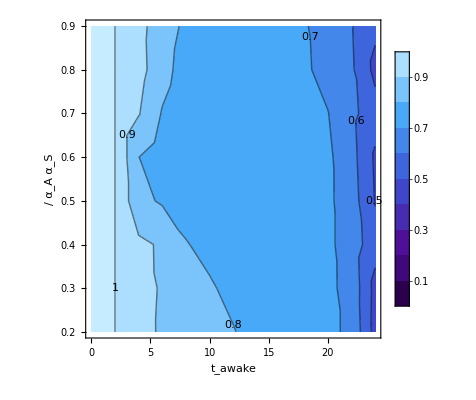

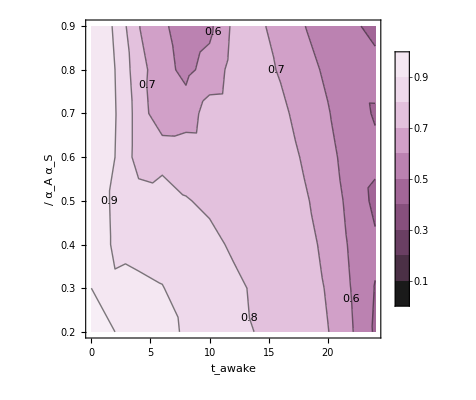

```mathematica
ListContourPlot[AvgAmountAI, 
Axes->False,
Frame->True,FrameLabel->{{Subscript["α","S"]"/"Subscript["α","A"]},{Subscript["t","awake"]}},
RotateLabel->True, 
ColorFunction->ColorData[{"DeepSeaColors",{0,1}}],
ColorFunctionScaling->False,
PlotRange->{0,1}, (*{{0,24},{0,2}},*)
 LabelStyle->{Directive[Black,22],FontFamily->"Times"},
InterpolationOrder->10,
AspectRatio->1, 
ContourLabels->True,
PlotLegends->Automatic
]

ListContourPlot[AvgAmountAV, 
Axes->False,
Frame->True,FrameLabel->{{Subscript["α","S"]"/"Subscript["α","A"]},{Subscript["t","awake"]}},
RotateLabel->True, 
ColorFunction->ColorData[{"FuchsiaTones",{0,1}}],
ColorFunctionScaling->False,
PlotRange->{0,1}, (*{{0,24},{0,2}},*)
 LabelStyle->{Directive[Black,22],FontFamily->"Times"},
InterpolationOrder->10,
AspectRatio->1, 
ContourLabels->True,
PlotLegends->Automatic
]
AvgFracAI
ListContourPlot[Floor[AvgFracAI*1000.]/1000., 
Axes->False,
Frame->True,FrameLabel->{{Subscript["α","S"]"/"Subscript["α","A"]},{Subscript["t","awake"]}},
RotateLabel->True, 
ColorFunction->ColorData[{"DeepSeaColors",{0,1}}],
ColorFunctionScaling->False,
PlotRange->{0,1}, (*{{0,24},{0,2}},*)
 LabelStyle->{Directive[Black,22],FontFamily->"Times"},
InterpolationOrder->10,
AspectRatio->1, 
ContourLabels->True,
PlotLegends->Automatic
]
(*PlotLegends->Placed[LineLegend[{{Red,Dashed},Red},{Subscript["v","eq"],Subscript["I","eq"]}], { Right,Top}]
PlotLegends->Placed[BarLegend[Automatic,Table[i,{i,0,1.1,0.1}], LegendMargins->{{0,0},{10,5}},LegendMarkerSize->250,
LegendLabel->Subscript["% time below I", "awake"],LabelStyle->{Italic,FontFamily->"Times"}],Above]*)
(*{Log[10,#1],Log[10,#2],#3}&@@@AvgFracAV,*)
Floor[AvgFracAV*1000.]/1000.
ListContourPlot[Floor[AvgFracAV*1000.]/1000., 
Axes->False,
Frame->True,FrameLabel->{{Subscript["α","S"]"/"Subscript["α","A"]},{Subscript["t","awake"]}},
RotateLabel->True, 
ColorFunction->ColorData[{"FuchsiaTones",{0,1}}],
ColorFunctionScaling->False,
PlotRange->{0,1}, (*{{0,24},{0,2}},*)
 LabelStyle->{Directive[Black,22],FontFamily->"Times"},
InterpolationOrder->10,
PlotLegends->Automatic,
AspectRatio->1 ,
(*PlotLegends->Placed[LineLegend[{{Red,Dashed},Red},{Subscript["v","eq"],Subscript["I","eq"]}], { Right,Top}]*)
ContourLabels->True]



(*PlotLegends->Placed[BarLegend[Automatic,{0.7,0.75,0.8,0.85,0.9,0.95},LegendMargins->{{0,0},{10,5}},LegendMarkerSize->250,LegendLabel->StringJoin["% of time below ", Subscript[v, awake]],LabelStyle->{Italic,FontFamily->"Times"}],Above]*)
```

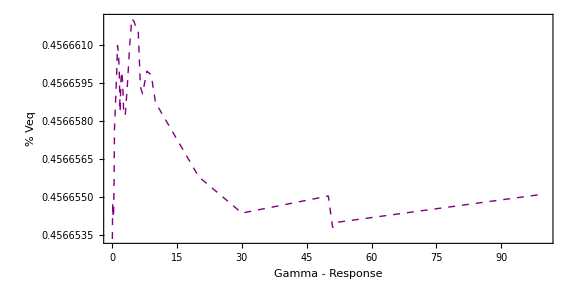

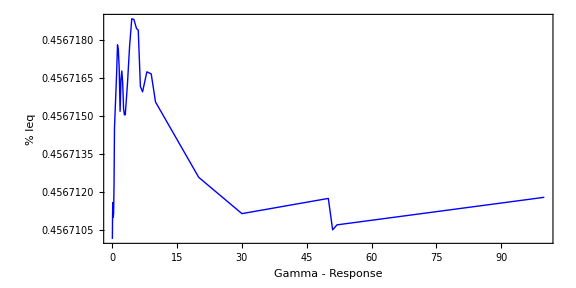

```mathematica
LmeanV=ListLinePlot[
    TemporalData[Transpose[AvgAmount[[2;;]]][[1]]/Transpose[InitConditAwakeAll[[2;;]]][[2]],{pars}],
AlignmentPoint->Center,
ImageSize->Large,
AspectRatio->0.5,Axes->True,(*AxesLabel->{"Virus","Immune"}*)
PlotRange->Full,(*{{0,All},{0.075,0.077}},Full,{0,All},{0,All}},*)
Frame->True,FrameStyle->Directive[10],
FrameLabel->{{Style["% Veq",18],None},{Style["Gamma - Response",18],None}},(*Axes->True,*)(*AxesLabel->{"Virus","Immune"},*)
PlotStyle->{Directive[Purple,Thick,Dashed]},FrameTicksStyle->Directive[Black,18]
]
LmeanI=ListLinePlot[TemporalData[Transpose[AvgAmount[[2;;]]][[2]]/Transpose[InitConditAwakeAll[[2;;]]][[1]],{pars}],AlignmentPoint->Center,ImageSize->Large,AspectRatio->0.5,PlotRange-> Full,(*{{0,All},{0.377,0.378}},*)
Frame->True,FrameStyle->Directive[10],FrameLabel->{{Style["% Ieq",18],None},{Style["Gamma - Response",18],None}},(*Axes->True,*)(*AxesLabel->{"Virus","Immune"},*)PlotStyle->{Directive[Blue,Thick]},FrameTicksStyle->Directive[Black,18]]
```

```mathematica
L3=ListLinePlot[TemporalData[{VirusData2,ImmuneData2}, {ttot2}],
	 AlignmentPoint->Center,
	ImageSize->Large,
	AspectRatio->0.5,
	Axes->True,
	AxesLabel->{"Virus","Immune"}
  PlotRange->{{0,All},{0,All}},
	Frame->True,FrameStyle->Directive[10],FrameLabel->{{Style["Concentration",18],None},{Style["Time [h]",18], None}},
	LabelStyle->{Directive[Black,22],FontFamily->"Times"},
	(*Axes->True,*)
	(*AxesLabel->{"Virus","Immune"}, *)
	PlotStyle->{Directive[Purple,Thick,Dashed],Directive[Blue,Thick]},
	FrameTicksStyle->Directive[Black,18],PlotLegends->Placed[LineLegend[{Directive[Purple,Thick,Dashed],Directive[Blue,Thick]},{"v(t)","I(t)"}], { Right,Top}]	
	(*{FontFamily->"Arial",FontSize->18,Black}*)
	];
```

```mathematica
MaxVirus=Max[N[IntegerPart[Max[VirusData]*12]/10],InitConditAwake[[2]]]
MaxImmune=Max[N[IntegerPart[Max[ImmuneData]*12]/10],InitConditAwake[[1]]]
MinVirus=N[IntegerPart[Min[VirusData]-0.1]]
MinImmune=N[IntegerPart[Min[ImmuneData]-0.1]]
```

1.1

2.5

0.

0.

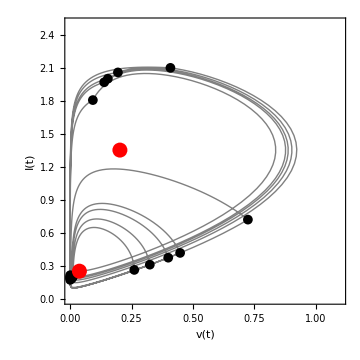

```mathematica
L1=ListLinePlot[Transpose[{VirusData,ImmuneData}],
	 AlignmentPoint->Center,
	Axes->False,Frame->True,FrameLabel->Join[{"v(t)","I(t)"},{None,None}],RotateLabel->True,
	(*ImageSize->Medium,
	AspectRatio->Full,
	Axes->True,
	AxesLabel->{"Virus","Immune"},*)
	Ticks->{Table[j,{j,0,MaxVirus,(MaxVirus)/5}],Table[j,{j,0, MaxImmune,MaxImmune/5}]},
	PlotStyle->{Directive[Gray,Thick]},
	PlotRange->{{0,MaxVirus},{0,MaxImmune}},
	PlotRangePadding->Scaled[.05],
	LabelStyle->{Directive[Black,22],FontFamily->"Times"},AspectRatio->1
	(*Frame->True,FrameStyle->Directive[10],FrameLabel->{{Style["Virus",18],None},{Style["Immune",18], None}},*)
	(*FrameTicks->{{Table[j,{j,0,MaxImmune,0.1}],None},{Table[j,{j,0,MaxVirus,0.1}],None}},*)
	(*Axes->True,*)
	(*AxesLabel->{"Virus","Immune"}, *)

	(*rameTicksStyle->Directive[Black,18]*)
	(*{FontFamily->"Arial",FontSize->18,Black}*)
	];
L2=ListPlot[TransPoint, PlotStyle->Directive[Large, Black],Axes->False,Frame->True,FrameLabel->Join[{"v(t)","I(t)"},{None,None}],RotateLabel->True, PlotRange->All,PlotRangePadding->0.1, LabelStyle->{Directive[Black,22],FontFamily->"Times"}, PlotStyle->{Directive[Gray,Thick]},  AspectRatio->1];
Leq=ListPlot[{Reverse[InitCondit0],Reverse[InitConditAwake]},PlotStyle->{PointSize[0.03],Red}];
Show[L1,L2, Leq]
```

```mathematica
(*Show[L4V,L3V]*)
(*Show[L3I,L4I]*)
```

```mathematica
L3=ListLinePlot[TemporalData[{VirusData2,ImmuneData2}, {ttot2}],
	 AlignmentPoint->Center,
	ImageSize->Large,
	AspectRatio->0.5,
	Axes->True,
	AxesLabel->{"Virus","Immune"}
  PlotRange->{{0,All},{0,All}},
	Frame->True,FrameStyle->Directive[10],FrameLabel->{{Style["Concentration",18],None},{Style["Time [h]",18], None}},
	LabelStyle->{Directive[Black,22],FontFamily->"Times"},
	(*Axes->True,*)
	(*AxesLabel->{"Virus","Immune"}, *)
	PlotStyle->{Directive[Purple,Thick,Dashed],Directive[Blue,Thick]},
	FrameTicksStyle->Directive[Black,18],PlotLegends->Placed[LineLegend[{Directive[Purple,Thick,Dashed],Directive[Blue,Thick]},{"v(t)","I(t)"}], { Right,Top}]	
	(*{FontFamily->"Arial",FontSize->18,Black}*)
	];
L4=ListPlot[TemporalData[TransPoint, {ttot}], PlotStyle->{Directive[Purple,Large],Directive[Blue,Large]}];
L4V2=ListPlot[TemporalData[TransPoint, {ttot}], PlotStyle->{Directive[Purple,Large],Directive[White,Large]}];
L4V=ListPlot[TemporalData[Transpose[TransPoint][[1]], {ttot}], PlotStyle->{Directive[Purple,Large]}, PlotRange->{{0,All},{0,All}}];
L4I=ListPlot[TemporalData[Transpose[TransPoint][[2]], {ttot}], PlotStyle->{Directive[Blue,Large]}];
```

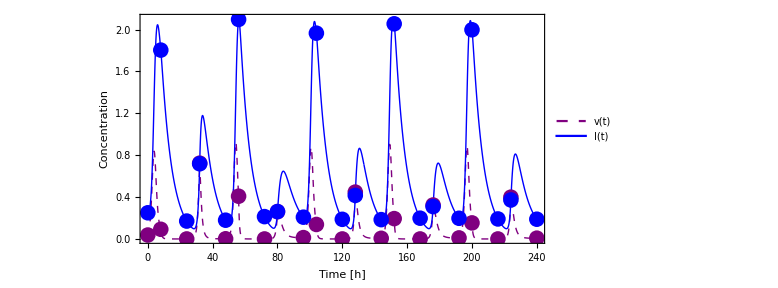

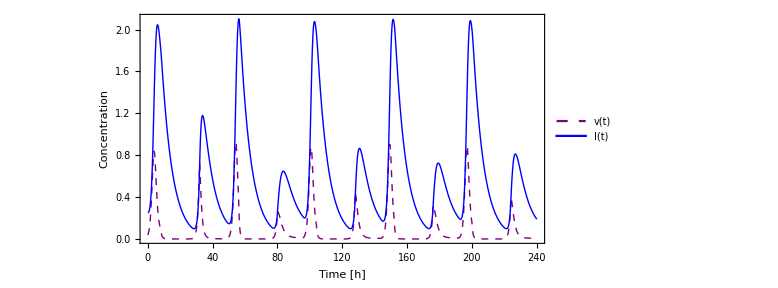

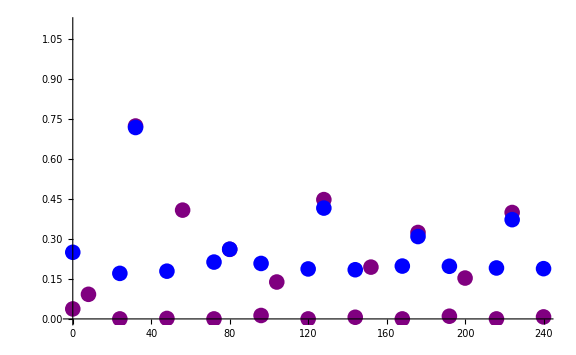

```mathematica
Show[L3,L4]
Show[L3]
Show[L4]
```